# Hands-on Start to Mathematica

## Basic Input

This example shows some simple arithmetic.

```mathematica
627/3
```

209

```mathematica
N[628/3]
```

209.333

graph sin(x)/x from -4Pi to 4Pi

-Graphics-

solve 2x-7=0 and 3x-2y=0 for x and y

{{x→7/2,y→21/4}}

picture of a caffiene molecule

-Graphics3D-

```mathematica
Plot[Sin[x]/x,{x,-4Pi,4Pi}]
```

-Graphics-

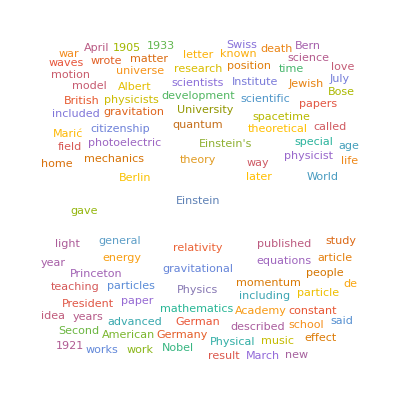

```mathematica
WordCloud[WikipediaData["Albert Einstein"]]
```

image of albert einstein

-Graphics-

```mathematica
FacialFeatures[Out[9]]
```

FacialFeatures::imginv: Expecting an image or graphics instead of %9.

FacialFeatures[%9]

## Rules of the Wolfram Language

Capital letters to start all function names

Function arguments are enclosed by square brackets [ ]

Lists (or ranges or domains) are enclosed by curly braces { }

Shift - Enter to do a calculation

## Multiple calculations & typesetting

```mathematica
∫(-10+x^2)ⅆx
```

-10 x+x^3/3

```mathematica
Factor[-10 x+x^3/3]
```

1/3 x (-30+x^2)

```mathematica
Plot[1/3 x (-30+x^2),{x,-13.416407864998739,13.416407864998739}]
```

-Graphics-

```mathematica
a=7;
b=3;
```

```mathematica
2 a + b
```

17

```mathematica
PrimeQ[17]
```

True

```mathematica
Clear[a,b]
```

```mathematica
mat1={{1,3,-2},{2,5,0},{-3,-5,7}}
```

{{1,3,-2},{2,5,0},{-3,-5,7}}

```mathematica
Det[mat1]
```

-17

```mathematica
IndependenceTest[mat1,3]
```

IndependenceTest::rctnln: The argument {{1,3,-2},{2,5,0},{-3,-5,7}} at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

IndependenceTest[{{1,3,-2},{2,5,0},{-3,-5,7}},3]

```mathematica
t=Table[InputFormAssistant,{i,1,5}]
ListPlot[t]
```

{1,4,9,16,25}

-Graphics-

## Link to AI and LLMs

## Options & Documentation

```mathematica
?Plot
```

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotHighlighting→None,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

## Interactive Models

```mathematica
Manipulate[Plot[Sin[freq x],{x,-5,5},PlotRange ->2],{freq,1,5}]
```

```mathematica
Manipulate[Plot[amp Sin[freq x],{x,-5,5},PlotRange ->2],{freq,1,5},{amp,0.5,2}]
```

```mathematica
Manipulate[Plot[amp func[freq x],{x,-5,5},PlotRange ->2],{freq,1,5},{amp,0.5,2},{func,{Sin,Cos,Tan,Cot,Sec,Csc,Tanh,Sinh,Cosh,Exp,ProductLog}}]
```

## Working with data

```mathematica
data1=Import["http://www.handsonstart.com/ExampleDataScores.csv"]
```

{{Joe,Smith,94},{Jane,Smith,85},{Bob,Example,82},{Bill,Student,83},{Michelle,Abacus,98}}

```mathematica
Dimensions[data1]
```

{5,3}

```mathematica
Part[data1,1]
```

{Joe,Smith,94}

```mathematica
Part[data1,All,3]
```

{94,85,82,83,98}

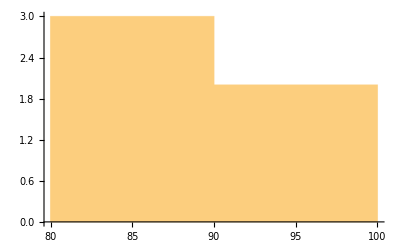

```mathematica
Histogram[Part[data1,All,3]]
```

```mathematica
data2=Import["ExampleData/50states.txt","Data"]
```

{Alabama,Alaska,Arizona,Arkansas,California,Colorado,Connecticut,Delaware,Florida,Georgia,Hawaii,Idaho,Illinois,Indiana,Iowa,Kansas,Kentucky,Louisiana,Maine,Maryland,Massachusetts,Michigan,Minnesota,Mississippi,Missouri,Montana,Nebraska,Nevada,New Hampshire,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oklahoma,Oregon,Pennsylvania,Rhode Island,South Carolina,South Dakota,Tennessee,Texas,Utah,Vermont,Virginia,Washington,West Virginia,Wisconsin,Wyoming}

```mathematica
Part[data2,{1,3}]
```

{Alabama,Arizona}

```mathematica
data3=Interpreter["USState"][data2]
```

{Alabama, United States,Alaska, United States,Arizona, United States,Arkansas, United States,California, United States,Colorado, United States,Connecticut, United States,Delaware, United States,Florida, United States,Georgia, United States,Hawaii, United States,Idaho, United States,Illinois, United States,Indiana, United States,Iowa, United States,Kansas, United States,Kentucky, United States,Louisiana, United States,Maine, United States,Maryland, United States,Massachusetts, United States,Michigan, United States,Minnesota, United States,Mississippi, United States,Missouri, United States,Montana, United States,Nebraska, United States,Nevada, United States,New Hampshire, United States,New Jersey, United States,New Mexico, United States,New York, United States,North Carolina, United States,North Dakota, United States,Ohio, United States,Oklahoma, United States,Oregon, United States,Pennsylvania, United States,Rhode Island, United States,South Carolina, United States,South Dakota, United States,Tennessee, United States,Texas, United States,Utah, United States,Vermont, United States,Virginia, United States,Washington, United States,West Virginia, United States,Wisconsin, United States,Wyoming, United States}

```mathematica
Part[data3,1]
```

Alabama, United States

```mathematica
AdministrativeDivisionData[Entity["AdministrativeDivision",{"Alabama","UnitedStates"}],"Population"]
```

5030053 people

```mathematica
AdministrativeDivisionData[Entity["AdministrativeDivision",{"Alabama","UnitedStates"}],"Area"]
```

52420.1 mi^2

```mathematica
Part[data3,1]["Properties"]
```

{accommodation and food services sales,number of aggravated assaults,rate of aggravated assault,aggregate household income,annual births,annual deaths,housing units change rate,area,average ACT composite score,average ACT English score,average ACT math score,average ACT reading score,average ACT science score,average commute time,average home sale price,average SAT reading score,average SAT evidence-based reading and writing score,average SAT math score,average SAT writing score,average total SAT score,bordering counties,bordering states,number of burglaries,rate of burglary,number of businesses,business ownership by ethnicity,Amerindian business ownership fraction,Asian business ownership fraction,black business ownership fraction,Hispanic business ownership fraction,Pacific Islander business ownership fraction,white business ownership fraction,business ownership by gender,capital city,capital name,civilian labor force,civilian unemployment rate,coincident economic activity index,coordinates,country,county sales tax rate,total rate of crime,total number of crimes,disabled people,district court,earnings,average earnings per job,employment,employment change,entity classes,entity type list,farmland area,federal government expenditure,federal government expenditure per capita,FIPS code,flag,image,number of rapes,rate of rape,fraction foreign born,high school graduates taking ACT,high school graduates taking SAT,Gini index,government employment,GDP,GSP,has polygon?,insured population fraction,people with health insurance,people without health insurance,uninsured population fraction,highest elevation,highest point,highest sales tax rate,home ownership rate,home vacancy rate,house price index,housing permits,housing starts,households,housing units change,housing in multiple unit structures,infant deaths,land area,number of larcenies,rate of larceny,latitude,longitude,lowest elevation,lowest point,lowest sales tax rate,manufacturing value of shipments,mean elevation,median age,median home listing price,median household income,median home sale price,median total sales tax rate,minimum wage,number of motor vehicle thefts,rate of motor vehicle thefts,state mottoes,incidents of murder and nonnegligent manslaughter,rate of murder and nonnegligent manslaughter,name,new housing units,new housing units value,state nicknames,nonemployer businesses,median owner-occupied home value,owner-occupied housing,parent region,per capita income,per capita personal income,people per household,polygon,population,population by educational attainment,population by migration in previous 12 months,population by language spoken at home,population by marital status,population by poverty status,population by school enrollment,population density,position,private non-farm employment,private non-farm employment change,private non-farm businesses,total rate of property crime,total number of property crimes,residential rental vacancy rate,4 bedroom apartment fair market rent,1 bedroom apartment fair market rent,3 bedroom apartment fair market rent,2 bedroom apartment fair market rent,studio apartment fair market rent,retail sales,retail sales per capita,number of robberies,rate of robbery,state slogan,state song,abbreviation,state government tax collections,state sales tax rate,subdivisions,time zones,total voter registration rate,total voting rate,state tree,unweighted sample housing units,unweighted sample population,total rate of violent crime,total number of violent crimes,wholesale sales,employment,ZIP codes}

## Sharing and deployments